## V to I Transfer Function

### Transfer function

#### Old:

```mathematica
Solve[(1/Rg+(1-g)/Rf) Zt==g-((g-1)/Rf+g/Rs) s L,{g}]
```

```mathematica
{{g->-(Rs (L Rg s-Rf Zt-Rg Zt))/(Rg (Rf Rs-L Rf s-L Rs s+Rs Zt))}}
```

{{g→-(Rs (L Rg s-Rf Zt-Rg Zt))/(Rg (Rf Rs-L Rf s-L Rs s+Rs Zt))}}

```mathematica
Zt[s_]:=Rt/(1+ⅈ s Rt Ct)
```

```mathematica
FullSimplify[(Zt[s]+(ⅈ L s/(g1)))/(Zt[s]+ⅈ L s g2+Rf)*(Conjugate[Zt[s]]-(ⅈ L s/(g1)))/(Conjugate[Zt[s]]-ⅈ L s g2+Rf),Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals}]
```

(L^2 s^2+Rt^2 (g1-Ct L s^2)^2)/(g1^2 (2 Rf Rt+g2^2 L^2 s^2+Rt^2 (-1+Ct g2 L s^2)^2+Rf^2 (1+Ct^2 Rt^2 s^2)))

```mathematica
G[s_,L_]:=Sqrt[(L^2 s^2+850000^2 (10-10^-12 L s^2)^2)/(2 866 850000+88^2 L^2 s^2+850000^2 (-1+10^-12 88 L s^2)^2+866^2 (1+(10^-12)^2 850000^2 s^2))]
```

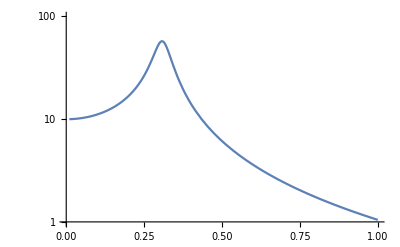

```mathematica
LogPlot[G[2 π f,300 10^-9],{f,10^6,10^8}, PlotRange->{1,100}]
```

#### Using Kirchoff, Rm = 0

```mathematica
(* Use Kirchoff's rules to get transfer function *)
Eliminate[Vo-Vs==Io s Lc&& Vs==Is Rs&&Vs-Vin==Iff Rf&&Io==Iff+Is&&Vo/(Rt/(1+s Rt Ct))+Iff==Ig&&Vin==Ig (Rg+s Lg),{Io,Is,Ig,Iff,Vo}]
(* With complex numbers *)
Eliminate[Vo-Vs==Io ⅈ s Lc&& Vs==Is Rs&&Vs-Vin==Iff Rf&&Io==Iff+Is&&Vo/(Rt/(1+ⅈ s Rt Ct))+Iff==Ig&&Vin==Ig (Rg+ⅈ s Lg),{Io,Is,Ig,Iff,Vo}]
```

Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3) Vin==(Rg Rs+(Rf Rg Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+(Lc Rf Rg s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rs s^3) Vs&&Rt≠0

Rs (-Rf-Rg-ⅈ Lg s-(ⅈ Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+ⅈ Ct Lc Lg s^3) Vin==(-Rg Rs-(Rf Rg Rs)/Rt-ⅈ Lg Rs s-ⅈ Ct Rf Rg Rs s-(ⅈ Lc Rf Rg s)/Rt-(ⅈ Lg Rf Rs s)/Rt-(ⅈ Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+ⅈ Ct Lc Lg Rf s^3+ⅈ Ct Lc Lg Rs s^3) Vs&&Rt≠0

```mathematica
Factor[Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3)/(Rg Rs+(Rf Rg Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+(Lc Rf Rg s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rs s^3)]
Factor[Rs (-Rf-Rg-ⅈ Lg s-(ⅈ Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+ⅈ Ct Lc Lg s^3)/(-Rg Rs-(Rf Rg Rs)/Rt-ⅈ Lg Rs s-ⅈ Ct Rf Rg Rs s-(ⅈ Lc Rf Rg s)/Rt-(ⅈ Lg Rf Rs s)/Rt-(ⅈ Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+ⅈ Ct Lc Lg Rf s^3+ⅈ Ct Lc Lg Rs s^3)]
```

(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/((Rg+Lg s) (Rf Rs+Rs Rt+Lc Rf s+Lc Rs s+Ct Rf Rs Rt s+Ct Lc Rf Rt s^2+Ct Lc Rs Rt s^2))

(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/((Rg+ⅈ Lg s) (Rf Rs+Rs Rt+ⅈ Lc Rf s+ⅈ Lc Rs s+ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2))

```mathematica
(* Transfer function without Lg *)
FullSimplify[(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/((Rg+Lg s) (Rf Rs+Rs Rt+Lc Rf s+Lc Rs s+Ct Rf Rs Rt s+Ct Lc Rf Rt s^2+Ct Lc Rs Rt s^2))/.Lg->0]
FullSimplify[(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/((Rg+ⅈ Lg s) (Rf Rs+Rs Rt+ⅈ Lc Rf s+ⅈ Lc Rs s+ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2))/.Lg->0]
```

(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Rg (Rf (Rs+Lc s) (1+Ct Rt s)+Rs (Rt+Lc s+Ct Lc Rt s^2)))

(Rs (-(Rf+Rg) Rt-ⅈ Lc Rg s+Ct Lc Rg Rt s^2))/(Rg (-Rs (Rf+Rt)-ⅈ (Lc (Rf+Rs)+Ct Rf Rs Rt) s+Ct Lc (Rf+Rs) Rt s^2))

```mathematica
(* Verify gain at DC is correct *)
Simplify[(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Rg (Rf (Rs+Lc s) (1+Ct Rt s)+Rs (Rt+Lc s+Ct Lc Rt s^2)))/.s->0]
Simplify[(-(Rf+Rg)-ⅈ Lc Rg s/Rt+Ct Lc Rg s^2)/(Rg (-(Rf/Rt+1)-ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2))/.s->0]
```

((Rf+Rg) Rt)/(Rg (Rf+Rt))

((Rf+Rg) Rt)/(Rg (Rf+Rt))

```mathematica
(* Verify that taking Lc/Rt -> 0 and Lc Ct -> 0 is valid *)
FullSimplify[Sqrt[(-(Rf+Rg)-ⅈ Lc Rg s/Rt+Ct Lc Rg s^2)/(Rg (-(Rf/Rt+1)-ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2)) (-(Rf+Rg)+ⅈ Lc Rg s/Rt+Ct Lc Rg s^2)/(Rg (-(Rf/Rt+1)+ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2))],Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals,Rg∈Reals,Rf∈Reals,Rs∈Reals,Lc∈Reals}]
```

√((Rs^2 (Rf Rt+Rg (Rt-ⅈ Lc s-Ct Lc Rt s^2)) (Rf Rt+Rg (Rt+ⅈ Lc s-Ct Lc Rt s^2)))/(Rg^2 (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4)))

```mathematica
(* Program and plot *)
G0[Rf_,Rg_,Rs_,Rt_,Lc_,Ct_,s_]:=√((Rs^2 (Rf Rt+Rg (Rt-ⅈ Lc s-Ct Lc Rt s^2)) (Rf Rt+Rg (Rt+ⅈ Lc s-Ct Lc Rt s^2)))/(Rg^2 (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4)));
```

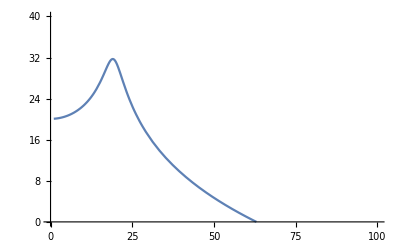

```mathematica
(* This looks like the simulation. *)
Plot[20 Log10[G0[215, 23.7, 10, 8.5*^5,3*^-7,1  10*^-12,2 π s 10^6]],{s,1,100},PlotRange->{0,40}]
```

```mathematica
Solve[Rf+Rg(1+ⅈ Lc s/Rt-Ct Lc s^2)==0,s](* zeros *)
Solve[(Rf/Rt+1)+ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s-Ct Lc (Rf/Rs+1) s^2==0,s](* poles *)
```

{{s→-(-√(4 Ct Lc Rg (Rf+Rg)-(Lc^2 Rg^2)/Rt^2)-(ⅈ Lc Rg)/Rt)/(2 Ct Lc Rg)},{s→-(√(4 Ct Lc Rg (Rf+Rg)-(Lc^2 Rg^2)/Rt^2)-(ⅈ Lc Rg)/Rt)/(2 Ct Lc Rg)}}

{{s→(ⅈ (Ct Rf-ⅈ √(-4 (-Ct Lc-(Ct Lc Rf)/Rs) (1+Rf/Rt)+(ⅈ Ct Rf+(ⅈ Lc)/Rt+(ⅈ Lc Rf)/(Rs Rt))^2)+Lc/Rt+(Lc Rf)/(Rs Rt)))/(2 (Ct Lc+(Ct Lc Rf)/Rs))},{s→(ⅈ (Ct Rf+ⅈ √(-4 (-Ct Lc-(Ct Lc Rf)/Rs) (1+Rf/Rt)+(ⅈ Ct Rf+(ⅈ Lc)/Rt+(ⅈ Lc Rf)/(Rs Rt))^2)+Lc/Rt+(Lc Rf)/(Rs Rt)))/(2 (Ct Lc+(Ct Lc Rf)/Rs))}}

```mathematica
(* Switch back to complex frequency *)
Solve[Rf+Rg(1+Lc s/Rt+Ct Lc s^2)==0,s](* zeros *)
Solve[(Rf/Rt+1)+(Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2==0,s](* poles *)
```

{{s→(-√(-4 Ct Lc Rg (Rf+Rg)+(Lc^2 Rg^2)/Rt^2)-(Lc Rg)/Rt)/(2 Ct Lc Rg)},{s→(√(-4 Ct Lc Rg (Rf+Rg)+(Lc^2 Rg^2)/Rt^2)-(Lc Rg)/Rt)/(2 Ct Lc Rg)}}

{{s→(-Ct Rf-√(-4 (Ct Lc+(Ct Lc Rf)/Rs) (1+Rf/Rt)+(Ct Rf+Lc/Rt+(Lc Rf)/(Rs Rt))^2)-Lc/Rt-(Lc Rf)/(Rs Rt))/(2 (Ct Lc+(Ct Lc Rf)/Rs))},{s→(-Ct Rf+√(-4 (Ct Lc+(Ct Lc Rf)/Rs) (1+Rf/Rt)+(Ct Rf+Lc/Rt+(Lc Rf)/(Rs Rt))^2)-Lc/Rt-(Lc Rf)/(Rs Rt))/(2 (Ct Lc+(Ct Lc Rf)/Rs))}}

```mathematica
(* Without Lg, I get nonsense values for the zeros that I'm supposedly compensating. I think I need to proceed with finding the poles and zeros of the full transfer function *)
```

```mathematica
FullSimplify[ComplexExpand[(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/((Rg+ⅈ Lg s) (Rf Rs+Rs Rt+ⅈ Lc Rf s+ⅈ Lc Rs s+ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2)) (Rs (Rf Rt+Rg Rt-ⅈ Lc Rg s-ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2+ⅈ Ct Lc Lg Rt s^3))/((Rg-ⅈ Lg s) (Rf Rs+Rs Rt-ⅈ Lc Rf s-ⅈ Lc Rs s-ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2))],Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals,Rg∈Reals,Rf∈Reals,Rs∈Reals,Lc∈Reals,Lg∈Reals}]
```

(Rs^2 (Rf^2 Rt^2+2 Rf Rt (Rg Rt-Lc (Lg+Ct Rg Rt) s^2)+(Rg^2+Lg^2 s^2) (Lc^2 s^2+Rt^2 (-1+Ct Lc s^2)^2)))/((Rg^2+Lg^2 s^2) (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4))

```mathematica
G1[Rf_,Rg_,Rs_,Rt_,Lc_,Lg_,Ct_,s_]:=Sqrt[(Rs^2 (Rf^2 Rt^2+2 Rf Rt (Rg Rt-Lc (Lg+Ct Rg Rt) s^2)+(Rg^2+Lg^2 s^2) (Lc^2 s^2+Rt^2 (-1+Ct Lc s^2)^2)))/((Rg^2+Lg^2 s^2) (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4))];
```

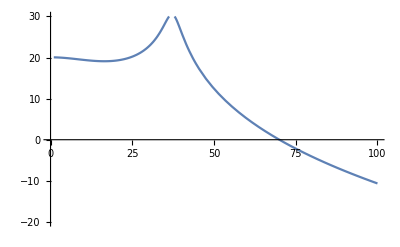

```mathematica
(* This looks like the simulation. *)
Plot[20 Log10[G1[215, 23.7, 8.33, 8.5*^5,2.7*^-7,2.2*^-7,.25  10*^-12,2 π s 10^6]],{s,1,100},PlotRange->{-20,30}]
```

```mathematica
Solve[Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3)==0,s]
Solve[(Rg+Lg s) (Rf Rs+Rs Rt+Lc Rf s+Lc Rs s+Ct Rf Rs Rt s+Ct Lc Rf Rt s^2+Ct Lc Rs Rt s^2) ==0,s]
```

{{s→-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)-(2^(1/3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))+1/(3 2^(1/3) Ct Lc Lg Rt)(-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)},{s→-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)+((1+ⅈ √3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 2^(2/3) Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))-1/(6 2^(1/3) Ct Lc Lg Rt)(1-ⅈ √3) (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)},{s→-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)+((1-ⅈ √3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 2^(2/3) Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))-1/(6 2^(1/3) Ct Lc Lg Rt)(1+ⅈ √3) (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)}}

{{s→-Rg/Lg},{s→(-Lc Rf-Lc Rs-Ct Rf Rs Rt-√(-4 (Rf Rs+Rs Rt) (Ct Lc Rf Rt+Ct Lc Rs Rt)+(Lc Rf+Lc Rs+Ct Rf Rs Rt)^2))/(2 (Ct Lc Rf Rt+Ct Lc Rs Rt))},{s→(-Lc Rf-Lc Rs-Ct Rf Rs Rt+√(-4 (Rf Rs+Rs Rt) (Ct Lc Rf Rt+Ct Lc Rs Rt)+(Lc Rf+Lc Rs+Ct Rf Rs Rt)^2))/(2 (Ct Lc Rf Rt+Ct Lc Rs Rt))}}

```mathematica
FullSimplify[-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)-(2^(1/3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))+1/(3 2^(1/3) Ct Lc Lg Rt)(-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)]
```

1/(6 Ct Lc Lg Rt)(-2 Lc (Lg+Ct Rg Rt)+(2 2^(1/3) Lc (Lc Lg^2-Ct Lc Lg Rg Rt+Ct (-3 Lg^2+Ct Lc Rg^2) Rt^2))/(-Lc^3 (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lc^2 Lg^2 Rt^2 (Lg-Ct (3 Rf+2 Rg) Rt)+√(Lc^3 (4 (3 Ct Lg Rt (Lc Rg+Lg Rt)-Lc (Lg+Ct Rg Rt)^2)^3+Lc (Lc (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lg^2 Rt^2 (-Lg+Ct (3 Rf+2 Rg) Rt))^2)))^(1/3)+2^(2/3) (-Lc^3 (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lc^2 Lg^2 Rt^2 (Lg-Ct (3 Rf+2 Rg) Rt)+√(Lc^3 (4 (3 Ct Lg Rt (Lc Rg+Lg Rt)-Lc (Lg+Ct Rg Rt)^2)^3+Lc (Lc (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lg^2 Rt^2 (-Lg+Ct (3 Rf+2 Rg) Rt))^2)))^(1/3))

#### Using Kirchoff, with Rm

```mathematica
(* Use Kirchoff's rules to get transfer function, including inverting input impedance *)
Eliminate[Vo-Vs==Io s Lc&& Vs==Is Rs&&Vs-Vm==Iff Rf&&Io==Iff+Is&&Vo/(Rt/(1+s Rt Ct))+Iff==Ig&&Vm==Ig (Rg+s Lg)&&Vin-Vm==Rm Vo/(Rt/(1+s Rt Ct)),{Io,Is,Ig,Iff,Vo, Vm}]
```

Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3) Vin==(Rg Rs+(Rf Rg Rs)/Rt+(Rf Rm Rs)/Rt+(Rg Rm Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+Ct Rf Rm Rs s+Ct Rg Rm Rs s+(Lc Rf Rg s)/Rt+(Lc Rf Rm s)/Rt+(Lc Rg Rm s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+(Lc Rm Rs s)/Rt+(Lg Rm Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lc Rf Rm s^2+Ct Lc Rg Rm s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+Ct Lc Rm Rs s^2+Ct Lg Rm Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rm s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rm s^3+Ct Lc Lg Rs s^3) Vs&&Rt≠0

```mathematica
Factor[Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3)/(Rg Rs+(Rf Rg Rs)/Rt+(Rf Rm Rs)/Rt+(Rg Rm Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+Ct Rf Rm Rs s+Ct Rg Rm Rs s+(Lc Rf Rg s)/Rt+(Lc Rf Rm s)/Rt+(Lc Rg Rm s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+(Lc Rm Rs s)/Rt+(Lg Rm Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lc Rf Rm s^2+Ct Lc Rg Rm s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+Ct Lc Rm Rs s^2+Ct Lg Rm Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rm s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rm s^3+Ct Lc Lg Rs s^3)]
```

(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)

```mathematica
(* Transfer function without Lg *)
FullSimplify[(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)/.Lg->0]
```

(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Lc Rm Rs s (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rg+Rm) (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))

```mathematica
(* Collect powers of s to put in standard form: *)
Collect[(Lc Rm Rs s (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rg+Rm) (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2)),s]
Collect[(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2))),s]
```

Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt+(Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt) s+(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt) s^2

Rs (Rf Rt+Rg Rt)+Lc Rg Rs s+Ct Lc Rg Rs Rt s^2

```mathematica
(* Simplify expression for omega_n *)
Simplify[(Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)]
```

(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/(Ct Lc (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)

```mathematica
(* Check numerics, it matches the jupyter code *)
wm=(Sqrt[(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/(Ct Lc (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)]/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5});
wm/(2 π 10^6)
```

38.1944

```mathematica
(* keep simplifying *)
FullSimplify[(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/((Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)]
```

(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/((Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)

```mathematica
(* check zeta, this should be 2*zeta*omega_n *)
Simplify[(Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)]
```

((Rg Rm+Rf (Rg+Rm)) Rs)/(Lc (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)))+1/(Ct Rt)

```mathematica
(* Square and divide by omega_n^2 for better simplification*)
FullSimplify[Sqrt[FullSimplify[Expand[(((Rg Rm+Rf (Rg+Rm)) Rs)/(Lc (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)))+1/(Ct Rt))^2/((Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/(Ct Lc (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt))]]]]/2
```

1/2 √((Lc (Rg Rm+Rf (Rg+Rm)+(Rg+Rm) Rs)+Ct (Rg Rm+Rf (Rg+Rm)) Rs Rt)^2/(Ct Lc Rs (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt (Rf (Rg+Rm)+Rg (Rm+Rt))))

```mathematica
zeta=(1/2 √((Lc (Rg Rm+Rf (Rg+Rm)+(Rg+Rm) Rs)+Ct (Rg Rm+Rf (Rg+Rm)) Rs Rt)^2/(Ct Lc Rs (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt (Rf (Rg+Rm)+Rg (Rm+Rt)))))/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5}
```

0.0644671

```mathematica
wd=wm*Sqrt[1-zeta^2]
```

38.115

```mathematica
(* Verify DC gain *)
FullSimplify[((Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Lc Rm Rs s (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rg+Rm) (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2)))/.s->0]
```

((Rf+Rg) Rt)/(Rf (Rg+Rm)+Rg (Rm+Rt))

```mathematica
(* Transfer function with Lg *)
FullSimplify[(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)]
```

(Rs (Rf Rt+(Rg+Lg s) (Rt+Lc s+Ct Lc Rt s^2)))/(Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))

```mathematica
Factor[(Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3

```mathematica
Collect[Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3,s]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+(Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt) s+(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt) s^2+(Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) s^3

```mathematica
Collect[(Rs (Rf Rt+(Rg+Lg s) (Rt+Lc s+Ct Lc Rt s^2))),s]
```

Rs (Rf Rt+Rg Rt)+Rs (Lc Rg+Lg Rt) s+Rs (Lc Lg+Ct Lc Rg Rt) s^2+Ct Lc Lg Rs Rt s^3

```mathematica
Collect[Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+(Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt) s+(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt) s^2+(Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) s^3,Lg]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lc Rg Rs s+Lc Rm Rs s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Lg (Rf Rs s+Rm Rs s+Rs Rt s+Lc Rf s^2+Lc Rm s^2+Lc Rs s^2+Ct Rf Rs Rt s^2+Ct Rm Rs Rt s^2+Ct Lc Rf Rt s^3+Ct Lc Rm Rt s^3+Ct Lc Rs Rt s^3)

```mathematica
Collect[FullSimplify[Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lc Rg Rs s+Lc Rm Rs s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Lg (Rf Rs s+Rm Rs s+Rs Rt s+Lc Rf s^2+Lc Rm s^2+Lc Rs s^2+Ct Rf Rs Rt s^2+Ct Rm Rs Rt s^2+Ct Lc Rf Rt s^3+Ct Lc Rm Rt s^3+Ct Lc Rs Rt s^3)],{Lg, s}]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+(Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lc Rg Rs+Lc Rm Rs+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt) s+(Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt) s^2+Lg ((Rf Rs+Rm Rs+Rs Rt) s+(Lc Rf+Lc (Rm+Rs)+Ct Rf Rs Rt+Ct Rm Rs Rt) s^2+(Ct Lc Rf Rt+Ct Lc (Rm+Rs) Rt) s^3)

```mathematica
Solve[Lc Rm Rs s (1+Ct Rt s)+Rf Rg (Rs+Lc s) (1+Ct Rt s)+Rf Rm (Rs+Lc s) (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2)+Lg (Lc (Rm+Rs) s^2 (1+Ct Rt s)+Rf s (Rs+Lc s) (1+Ct Rt s)+Rs s (Rm+Rt+Ct Rm Rt s))==0,s]
```

{{s→-((Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)/(3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt)))-(2^(1/3) (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt)))/(3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) ((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3+√(((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3))^2+4 (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt))^3)))^(1/3))+((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3+√(((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3))^2+4 (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt))^3)))^(1/3)/(3 2^(1/3) (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt))},{s→-((Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)/(3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt)))+((1+ⅈ √3) (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt)))/(3 2^(2/3) (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) ((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3+√(((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3))^2+4 (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt))^3)))^(1/3))-((1-ⅈ √3) ((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3+√(((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3))^2+4 (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt))^3)))^(1/3))/(6 2^(1/3) (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt))},{s→-((Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)/(3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt)))+((1-ⅈ √3) (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt)))/(3 2^(2/3) (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) ((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3+√(((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3))^2+4 (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt))^3)))^(1/3))-((1+ⅈ √3) ((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3+√(((-2 Lc^3 Lg^3 Rf^3-6 Lc^3 Lg^3 Rf^2 Rm-6 Lc^3 Lg^3 Rf Rm^2-2 Lc^3 Lg^3 Rm^3-6 Lc^3 Lg^3 Rf^2 Rs-12 Lc^3 Lg^3 Rf Rm Rs-6 Lc^3 Lg^3 Rm^2 Rs-6 Lc^3 Lg^3 Rf Rs^2-6 Lc^3 Lg^3 Rm Rs^2-2 Lc^3 Lg^3 Rs^3+3 Ct Lc^3 Lg^2 Rf^3 Rg Rt+3 Ct Lc^3 Lg^2 Rf^3 Rm Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rm Rt+6 Ct Lc^3 Lg^2 Rf^2 Rm^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rm^2 Rt+3 Ct Lc^3 Lg^2 Rf Rm^3 Rt+3 Ct Lc^3 Lg^2 Rg Rm^3 Rt+3 Ct Lc^2 Lg^3 Rf^3 Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rg Rs Rt+9 Ct Lc^3 Lg^2 Rf^2 Rm Rs Rt+9 Ct Lc^2 Lg^3 Rf^2 Rm Rs Rt+18 Ct Lc^3 Lg^2 Rf Rg Rm Rs Rt+12 Ct Lc^3 Lg^2 Rf Rm^2 Rs Rt+9 Ct Lc^2 Lg^3 Rf Rm^2 Rs Rt+9 Ct Lc^3 Lg^2 Rg Rm^2 Rs Rt+3 Ct Lc^3 Lg^2 Rm^3 Rs Rt+3 Ct Lc^2 Lg^3 Rm^3 Rs Rt+6 Ct Lc^2 Lg^3 Rf^2 Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rg Rs^2 Rt+9 Ct Lc^3 Lg^2 Rf Rm Rs^2 Rt+12 Ct Lc^2 Lg^3 Rf Rm Rs^2 Rt+9 Ct Lc^3 Lg^2 Rg Rm Rs^2 Rt+6 Ct Lc^3 Lg^2 Rm^2 Rs^2 Rt+6 Ct Lc^2 Lg^3 Rm^2 Rs^2 Rt+3 Ct Lc^2 Lg^3 Rf Rs^3 Rt+3 Ct Lc^3 Lg^2 Rg Rs^3 Rt+3 Ct Lc^3 Lg^2 Rm Rs^3 Rt+3 Ct Lc^2 Lg^3 Rm Rs^3 Rt+3 Ct^2 Lc^3 Lg Rf^3 Rg^2 Rt^2+6 Ct^2 Lc^3 Lg Rf^3 Rg Rm Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rm Rt^2+3 Ct^2 Lc^3 Lg Rf^3 Rm^2 Rt^2+12 Ct^2 Lc^3 Lg Rf^2 Rg Rm^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rm^2 Rt^2+3 Ct^2 Lc^3 Lg Rf^2 Rm^3 Rt^2+6 Ct^2 Lc^3 Lg Rf Rg Rm^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rm^3 Rt^2+9 Ct Lc^2 Lg^3 Rf^2 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rg Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rg^2 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rm Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf^3 Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf^2 Rg Rm Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rm Rs Rt^2+18 Ct^2 Lc^3 Lg Rf Rg^2 Rm Rs Rt^2+9 Ct Lc^2 Lg^3 Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rf^2 Rm^2 Rs Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm^2 Rs Rt^2+24 Ct^2 Lc^3 Lg Rf Rg Rm^2 Rs Rt^2-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm^2 Rs Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm^2 Rs Rt^2+6 Ct^2 Lc^3 Lg Rf Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm^3 Rs Rt^2+6 Ct^2 Lc^3 Lg Rg Rm^3 Rs Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm^3 Rs Rt^2+18 Ct Lc^2 Lg^3 Rf Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rf^3 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rg^2 Rs^2 Rt^2+18 Ct Lc^2 Lg^3 Rm Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf^2 Rm Rs^2 Rt^2+18 Ct^2 Lc^3 Lg Rf Rg Rm Rs^2 Rt^2-48 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rg^2 Rm Rs^2 Rt^2+9 Ct^2 Lc^3 Lg Rf Rm^2 Rs^2 Rt^2-18 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs^2 Rt^2+9 Ct^2 Lc Lg^3 Rf Rm^2 Rs^2 Rt^2+12 Ct^2 Lc^3 Lg Rg Rm^2 Rs^2 Rt^2-24 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs^2 Rt^2+3 Ct^2 Lc^3 Lg Rm^3 Rs^2 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^3 Rs^2 Rt^2+3 Ct^2 Lc Lg^3 Rm^3 Rs^2 Rt^2+9 Ct Lc^2 Lg^3 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rf^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rg Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc Lg^3 Rf Rm Rs^3 Rt^2+6 Ct^2 Lc^3 Lg Rg Rm Rs^3 Rt^2-12 Ct^2 Lc^2 Lg^2 Rg Rm Rs^3 Rt^2+3 Ct^2 Lc^3 Lg Rm^2 Rs^3 Rt^2+6 Ct^2 Lc^2 Lg^2 Rm^2 Rs^3 Rt^2+3 Ct^2 Lc Lg^3 Rm^2 Rs^3 Rt^2-2 Ct^3 Lc^3 Rf^3 Rg^3 Rt^3-6 Ct^3 Lc^3 Rf^3 Rg^2 Rm Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rm Rt^3-6 Ct^3 Lc^3 Rf^3 Rg Rm^2 Rt^3-12 Ct^3 Lc^3 Rf^2 Rg^2 Rm^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rm^2 Rt^3-2 Ct^3 Lc^3 Rf^3 Rm^3 Rt^3-6 Ct^3 Lc^3 Rf^2 Rg Rm^3 Rt^3-6 Ct^3 Lc^3 Rf Rg^2 Rm^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rm^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rf^2 Rg Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rg^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rg^3 Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf^2 Rm Rs Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rm Rs Rt^3+6 Ct^3 Lc^2 Lg Rf^3 Rg Rm Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg^2 Rm Rs Rt^3+9 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rm Rs Rt^3-12 Ct^3 Lc^3 Rf Rg^3 Rm Rs Rt^3+9 Ct^2 Lc^2 Lg^2 Rf Rm^2 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^3 Rm^2 Rs Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rm^2 Rs Rt^3-18 Ct^3 Lc^3 Rf^2 Rg Rm^2 Rs Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm^2 Rs Rt^3-24 Ct^3 Lc^3 Rf Rg^2 Rm^2 Rs Rt^3+9 Ct^3 Lc^2 Lg Rf Rg^2 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rg^3 Rm^2 Rs Rt^3-6 Ct^3 Lc^3 Rf^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rf^2 Rm^3 Rs Rt^3-12 Ct^3 Lc^3 Rf Rg Rm^3 Rs Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm^3 Rs Rt^3-6 Ct^3 Lc^3 Rg^2 Rm^3 Rs Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm^3 Rs Rt^3+9 Ct^2 Lc Lg^3 Rf^2 Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rf Rg Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rg Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rg^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rg^3 Rs^2 Rt^3+18 Ct^2 Lc^2 Lg^2 Rf Rm Rs^2 Rt^3+18 Ct^2 Lc Lg^3 Rf Rm Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf^3 Rm Rs^2 Rt^3-36 Ct^2 Lc^2 Lg^2 Rg Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf^2 Rg Rm Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf^2 Rg Rm Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg^2 Rm Rs^2 Rt^3+12 Ct^3 Lc^2 Lg Rf Rg^2 Rm Rs^2 Rt^3-6 Ct^3 Lc^3 Rg^3 Rm Rs^2 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm^2 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rf^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc Lg^2 Rf^2 Rm^2 Rs^2 Rt^3-18 Ct^3 Lc^3 Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc^2 Lg Rf Rg Rm^2 Rs^2 Rt^3+9 Ct^3 Lc Lg^2 Rf Rg Rm^2 Rs^2 Rt^3-12 Ct^3 Lc^3 Rg^2 Rm^2 Rs^2 Rt^3+6 Ct^3 Lc^2 Lg Rg^2 Rm^2 Rs^2 Rt^3-6 Ct^3 Lc^3 Rf Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rf Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rf Rm^3 Rs^2 Rt^3-6 Ct^3 Lc^3 Rg Rm^3 Rs^2 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^3 Rs^2 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^3 Rs^2 Rt^3+9 Ct^2 Lc Lg^3 Rf Rs^3 Rt^3-2 Ct^3 Lg^3 Rf^3 Rs^3 Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rg Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rg^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rg^3 Rs^3 Rt^3+9 Ct^2 Lc^2 Lg^2 Rm Rs^3 Rt^3+9 Ct^2 Lc Lg^3 Rm Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rf^2 Rm Rs^3 Rt^3-6 Ct^3 Lg^3 Rf^2 Rm Rs^3 Rt^3+6 Ct^3 Lc^2 Lg Rf Rg Rm Rs^3 Rt^3+6 Ct^3 Lc Lg^2 Rf Rg Rm Rs^3 Rt^3-6 Ct^3 Lc^3 Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rg^2 Rm Rs^3 Rt^3+3 Ct^3 Lc^2 Lg Rf Rm^2 Rs^3 Rt^3-3 Ct^3 Lc Lg^2 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lg^3 Rf Rm^2 Rs^3 Rt^3-6 Ct^3 Lc^3 Rg Rm^2 Rs^3 Rt^3-3 Ct^3 Lc^2 Lg Rg Rm^2 Rs^3 Rt^3+3 Ct^3 Lc Lg^2 Rg Rm^2 Rs^3 Rt^3-2 Ct^3 Lc^3 Rm^3 Rs^3 Rt^3-6 Ct^3 Lc^2 Lg Rm^3 Rs^3 Rt^3-6 Ct^3 Lc Lg^2 Rm^3 Rs^3 Rt^3-2 Ct^3 Lg^3 Rm^3 Rs^3 Rt^3))^2+4 (-(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt)^2+3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) (Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt))^3)))^(1/3))/(6 2^(1/3) (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt))}}

```mathematica
((Rs (Rf Rt+(Rg+Lg s) (Rt+Lc s+Ct Lc Rt s^2)))/(Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2)))/.s->ⅈ s
```

(Rs (Rf Rt+(Rg+ⅈ Lg s) (Rt+ⅈ Lc s-Ct Lc Rt s^2)))/(Rg Rm (Rs+ⅈ Lc s) (1+ⅈ Ct Rt s)+Rf (Rs+ⅈ Lc s) (Rg+Rm+ⅈ Lg s) (1+ⅈ Ct Rt s)+ⅈ Lc s (Rm Rs+ⅈ Lg (Rm+Rs) s) (1+ⅈ Ct Rt s)+ⅈ Lg Rs s (Rm+Rt+ⅈ Ct Rm Rt s)+Rg Rs (Rt+ⅈ Lc s-Ct Lc Rt s^2))

```mathematica
FullSimplify[ComplexExpand[((Rs (Rf Rt+(Rg+ⅈ Lg s) (Rt+ⅈ Lc s-Ct Lc Rt s^2)))/(Rg Rm (Rs+ⅈ Lc s) (1+ⅈ Ct Rt s)+Rf (Rs+ⅈ Lc s) (Rg+Rm+ⅈ Lg s) (1+ⅈ Ct Rt s)+ⅈ Lc s (Rm Rs+ⅈ Lg (Rm+Rs) s) (1+ⅈ Ct Rt s)+ⅈ Lg Rs s (Rm+Rt+ⅈ Ct Rm Rt s)+Rg Rs (Rt+ⅈ Lc s-Ct Lc Rt s^2))) ((Rs (Rf Rt+(Rg-ⅈ Lg s) (Rt-ⅈ Lc s-Ct Lc Rt s^2)))/(Rg Rm (Rs-ⅈ Lc s) (1-ⅈ Ct Rt s)+Rf (Rs-ⅈ Lc s) (Rg+Rm-ⅈ Lg s) (1-ⅈ Ct Rt s)-ⅈ Lc s (Rm Rs-ⅈ Lg (Rm+Rs) s) (1-ⅈ Ct Rt s)-ⅈ Lg Rs s (Rm+Rt-ⅈ Ct Rm Rt s)+Rg Rs (Rt-ⅈ Lc s-Ct Lc Rt s^2)))],Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals,Rg∈Reals,Rf∈Reals,Rs∈Reals,Lc∈Reals, Lg∈Reals, Rm∈Reals}]
```

(Rs^2 (Rf^2 Rt^2+2 Rf Rt (Rg Rt-Lc (Lg+Ct Rg Rt) s^2)+(Rg^2+Lg^2 s^2) (Lc^2 s^2+Rt^2 (-1+Ct Lc s^2)^2)))/(Rg^2 Rs^2 (Rm+Rt)^2+((Lc Rg Rm+Lc (Rg+Rm) Rs)^2+2 Lc Rs (-Ct Rg (Rg Rm+(Rg+Rm) Rs) Rt^2+Lg Rm Rs (Rm+Rt))+Rs^2 (Ct^2 Rg^2 Rm^2 Rt^2+Lg^2 (Rm+Rt)^2)) s^2+(Lc^2 Lg^2 (Rm+Rs)^2+Ct (-2 Lc Lg^2 Rs (Rm+Rs)+Ct (2 Lc Lg Rm^2 Rs^2+Lg^2 Rm^2 Rs^2+(Lc Rg Rm+Lc (Rg+Rm) Rs)^2)) Rt^2) s^4+Ct^2 Lc^2 Lg^2 (Rm+Rs)^2 Rt^2 s^6+Rf^2 (Rs^2+Lc^2 s^2) ((Rg+Rm)^2+Lg^2 s^2) (1+Ct^2 Rt^2 s^2)+2 Rf (Rg (Rg+Rm) Rs^2 (Rm+Rt)+(Lc^2 (Rg+Rm) (Rm Rs+Rg (Rm+Rs))+Lc Rs Rt (Lg Rm-Ct Rg (Rg+Rm) Rt)+Rs^2 (Lg^2 Rm+Lg^2 Rt+Ct Rm (Lg+Ct Rg (Rg+Rm)) Rt^2)) s^2+(Lc^2 Lg^2 (Rm+Rs)+Ct (-Lc Lg^2 Rs+Ct Lg^2 Rm Rs^2+Ct Lc^2 (Rg+Rm) (Rm Rs+Rg (Rm+Rs))) Rt^2) s^4+Ct^2 Lc^2 Lg^2 (Rm+Rs) Rt^2 s^6))

```mathematica
(((Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt))/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5})/wm^2
(((Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt))/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5})/(2*zeta*wm)
```

1.

1.

```mathematica
(* Switch to numerics *)
a0=Rs (Rf Rt+Rg Rt)/.{Rs->8.33,Rg->23.7,Rf->215,Rt->8.5*10^5}
a1=(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5}
Y[s_]:=Abs[a0/a1/(s^2+2*zeta*wm*s+wm^2)]
Y1[s_]:=Abs[((Rs (Rf Rt+Rg Rt))/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt))/((Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)+(Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt) s/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)+ s^2)]/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5}
Y2[s_]:=Abs[(Rs (Rf Rt+(Rg+Lg s) (Rt+Lc s+Ct Lc Rt s^2)))/(Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))]/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5,Lg->2.2*10^-7}
```

1.69012×10^9

2.91553×10^-9

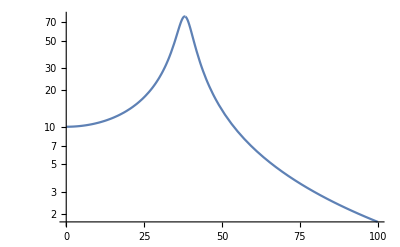

```mathematica
(* This looks like the simulation, but Cp has to be very small*)
LogPlot[{Y[2 π ⅈ s 10^6]},{s,0,100}]
```

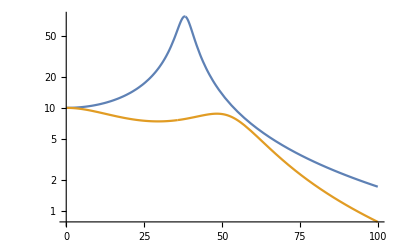

```mathematica
LogPlot[{Y1[2 π ⅈ s 10^6],Y2[2 π ⅈ s 10^6],Y[2 π ⅈ s 10^6]},{s,0,100}]
```

```mathematica
Solve[((Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5,Lg->2.2*10^-7})==0,s]
Solve[(((Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)+(Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt) s/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)+ s^2)/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5})==0,s]
```

{{s→-1.16933×10^8},{s→-7.10118×10^7-3.2745×10^8 ⅈ},{s→-7.10118×10^7+3.2745×10^8 ⅈ}}

{{s→-1.5471×10^7-2.39483×10^8 ⅈ},{s→-1.5471×10^7+2.39483×10^8 ⅈ}}

```mathematica
(* Natural Freq. with Lg = 0 *)
Abs[-1.5470990735264925*^7-2.3948335665996426*^8 ⅈ]/2/π/10^6
(* Natural Freq with Lg ≠ 0 *)
Abs[-7.101180049729846*^7-3.274499225421783*^8 ⅈ]/2/π/10^6
(* Damped pole freq. *)
Abs[-1.1693262174614537*^8]/2/π/10^6
Rg/Lg/2/π/10^6/.{Lg->2.2 10^-7,Rg->23.7}
```

38.1944

53.3267

18.6104

17.1453

```mathematica
Solve[((Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5,Lg->1.8*10^-7})==0,s]
Solve[(((Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)+(Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt) s/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)+ s^2)/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5})==0,s]
```

{{s→-1.50665×10^8},{s→-7.94725×10^7-3.16508×10^8 ⅈ},{s→-7.94725×10^7+3.16508×10^8 ⅈ}}

{{s→-1.5471×10^7-2.39483×10^8 ⅈ},{s→-1.5471×10^7+2.39483×10^8 ⅈ}}

```mathematica
(* Natural Freq. with Lg = 0 *)
Abs[-1.5470990735264925*^7-2.3948335665996426*^8 ⅈ]/2/π/10^6
(* Natural Freq with Lg ≠ 0 *)
Abs[-6.903107427609076*^7-2.5433637409534222*^8 ⅈ]/2/π/10^6
(* Damped pole freq. *)
Abs[-5.197932238783292*^8]/2/π/10^6
Rg/Lg/2/π/10^6/.{Lg->1.8 10^-7,Rg->23.7}
```

38.1944

41.9434

82.7277

47.1497

#### Add Cp

```mathematica
(* Use Kirchoff's rules to get transfer function, including inverting input impedance *)
Eliminate[Vo-Vs==Ic s Lc&&Vo-Vs==Ip/(s Cp)&& Vs==Is Rs&&Vs-Vm==Iff Rf&&Ic+Ip==Iff+Is&&Vo/(Rt/(1+s Rt Ct))+Iff==Ig&&Vm==Ig (Rg+s Lg)&&Vin-Vm==Rm Vo/(Rt/(1+s Rt Ct)),{Ic,Ip,Is,Ig,Iff,Vo, Vm}]
```

Rs (Cp Lc Rf+Cp Lc Rg+Ct Lc Rg+(Lc Lg)/Rt+Rf/s^2+Rg/s^2+Lg/s+(Lc Rg)/(Rt s)+Cp Lc Lg s+Ct Lc Lg s) Vin==(Ct Lc Rf Rg+Ct Lc Rf Rm+Ct Lc Rg Rm+Ct Lg Rf Rs+Cp Lc Rg Rs+Ct Lc Rg Rs+Ct Lc Rm Rs+Ct Lg Rm Rs+(Lc Lg Rf)/Rt+(Lc Lg Rm)/Rt+(Lc Lg Rs)/Rt+(Cp Lc Rf Rg Rs)/Rt+(Cp Lc Rf Rm Rs)/Rt+(Cp Lc Rg Rm Rs)/Rt+(Rg Rs)/s^2+(Rf Rg Rs)/(Rt s^2)+(Rf Rm Rs)/(Rt s^2)+(Rg Rm Rs)/(Rt s^2)+(Lg Rs)/s+(Ct Rf Rg Rs)/s+(Ct Rf Rm Rs)/s+(Ct Rg Rm Rs)/s+(Lc Rf Rg)/(Rt s)+(Lc Rf Rm)/(Rt s)+(Lc Rg Rm)/(Rt s)+(Lg Rf Rs)/(Rt s)+(Lc Rg Rs)/(Rt s)+(Lc Rm Rs)/(Rt s)+(Lg Rm Rs)/(Rt s)+Ct Lc Lg Rf s+Ct Lc Lg Rm s+Cp Lc Lg Rs s+Ct Lc Lg Rs s+Cp Ct Lc Rf Rg Rs s+Cp Ct Lc Rf Rm Rs s+Cp Ct Lc Rg Rm Rs s+(Cp Lc Lg Rf Rs s)/Rt+(Cp Lc Lg Rm Rs s)/Rt+Cp Ct Lc Lg Rf Rs s^2+Cp Ct Lc Lg Rm Rs s^2) Vs&&Rs (Lc Rf+Lc Rg+(Ct Lc Rg)/Cp+(Lc Lg)/(Cp Rt)+Rf/(Cp s^2)+Rg/(Cp s^2)+Lg/(Cp s)+(Lc Rg)/(Cp Rt s)+Lc Lg s+(Ct Lc Lg s)/Cp) Vin==((Ct Lc Rf Rg)/Cp+(Ct Lc Rf Rm)/Cp+(Ct Lc Rg Rm)/Cp+(Ct Lg Rf Rs)/Cp+Lc Rg Rs+(Ct Lc Rg Rs)/Cp+(Ct Lc Rm Rs)/Cp+(Ct Lg Rm Rs)/Cp+(Lc Lg Rf)/(Cp Rt)+(Lc Lg Rm)/(Cp Rt)+(Lc Lg Rs)/(Cp Rt)+(Lc Rf Rg Rs)/Rt+(Lc Rf Rm Rs)/Rt+(Lc Rg Rm Rs)/Rt+(Rg Rs)/(Cp s^2)+(Rf Rg Rs)/(Cp Rt s^2)+(Rf Rm Rs)/(Cp Rt s^2)+(Rg Rm Rs)/(Cp Rt s^2)+(Lg Rs)/(Cp s)+(Ct Rf Rg Rs)/(Cp s)+(Ct Rf Rm Rs)/(Cp s)+(Ct Rg Rm Rs)/(Cp s)+(Lc Rf Rg)/(Cp Rt s)+(Lc Rf Rm)/(Cp Rt s)+(Lc Rg Rm)/(Cp Rt s)+(Lg Rf Rs)/(Cp Rt s)+(Lc Rg Rs)/(Cp Rt s)+(Lc Rm Rs)/(Cp Rt s)+(Lg Rm Rs)/(Cp Rt s)+(Ct Lc Lg Rf s)/Cp+(Ct Lc Lg Rm s)/Cp+Lc Lg Rs s+(Ct Lc Lg Rs s)/Cp+Ct Lc Rf Rg Rs s+Ct Lc Rf Rm Rs s+Ct Lc Rg Rm Rs s+(Lc Lg Rf Rs s)/Rt+(Lc Lg Rm Rs s)/Rt+Ct Lc Lg Rf Rs s^2+Ct Lc Lg Rm Rs s^2) Vs&&Cp≠0&&Rt≠0&&s≠0

```mathematica
(* Consistency check *)
FullSimplify[(Cp Lc Rf+Cp Lc Rg+Ct Lc Rg+(Lc Lg)/Rt+Rf/s^2+Rg/s^2+Lg/s+(Lc Rg)/(Rt s)+Cp Lc Lg s+Ct Lc Lg s) /(Lc Rf+Lc Rg+(Ct Lc Rg)/Cp+(Lc Lg)/(Cp Rt)+Rf/(Cp s^2)+Rg/(Cp s^2)+Lg/(Cp s)+(Lc Rg)/(Cp Rt s)+Lc Lg s+(Ct Lc Lg s)/Cp)]
```

Cp

```mathematica
(* Consistency check *)
FullSimplify[(Ct Lc Rf Rg+Ct Lc Rf Rm+Ct Lc Rg Rm+Ct Lg Rf Rs+Cp Lc Rg Rs+Ct Lc Rg Rs+Ct Lc Rm Rs+Ct Lg Rm Rs+(Lc Lg Rf)/Rt+(Lc Lg Rm)/Rt+(Lc Lg Rs)/Rt+(Cp Lc Rf Rg Rs)/Rt+(Cp Lc Rf Rm Rs)/Rt+(Cp Lc Rg Rm Rs)/Rt+(Rg Rs)/s^2+(Rf Rg Rs)/(Rt s^2)+(Rf Rm Rs)/(Rt s^2)+(Rg Rm Rs)/(Rt s^2)+(Lg Rs)/s+(Ct Rf Rg Rs)/s+(Ct Rf Rm Rs)/s+(Ct Rg Rm Rs)/s+(Lc Rf Rg)/(Rt s)+(Lc Rf Rm)/(Rt s)+(Lc Rg Rm)/(Rt s)+(Lg Rf Rs)/(Rt s)+(Lc Rg Rs)/(Rt s)+(Lc Rm Rs)/(Rt s)+(Lg Rm Rs)/(Rt s)+Ct Lc Lg Rf s+Ct Lc Lg Rm s+Cp Lc Lg Rs s+Ct Lc Lg Rs s+Cp Ct Lc Rf Rg Rs s+Cp Ct Lc Rf Rm Rs s+Cp Ct Lc Rg Rm Rs s+(Cp Lc Lg Rf Rs s)/Rt+(Cp Lc Lg Rm Rs s)/Rt+Cp Ct Lc Lg Rf Rs s^2+Cp Ct Lc Lg Rm Rs s^2)/((Ct Lc Rf Rg)/Cp+(Ct Lc Rf Rm)/Cp+(Ct Lc Rg Rm)/Cp+(Ct Lg Rf Rs)/Cp+Lc Rg Rs+(Ct Lc Rg Rs)/Cp+(Ct Lc Rm Rs)/Cp+(Ct Lg Rm Rs)/Cp+(Lc Lg Rf)/(Cp Rt)+(Lc Lg Rm)/(Cp Rt)+(Lc Lg Rs)/(Cp Rt)+(Lc Rf Rg Rs)/Rt+(Lc Rf Rm Rs)/Rt+(Lc Rg Rm Rs)/Rt+(Rg Rs)/(Cp s^2)+(Rf Rg Rs)/(Cp Rt s^2)+(Rf Rm Rs)/(Cp Rt s^2)+(Rg Rm Rs)/(Cp Rt s^2)+(Lg Rs)/(Cp s)+(Ct Rf Rg Rs)/(Cp s)+(Ct Rf Rm Rs)/(Cp s)+(Ct Rg Rm Rs)/(Cp s)+(Lc Rf Rg)/(Cp Rt s)+(Lc Rf Rm)/(Cp Rt s)+(Lc Rg Rm)/(Cp Rt s)+(Lg Rf Rs)/(Cp Rt s)+(Lc Rg Rs)/(Cp Rt s)+(Lc Rm Rs)/(Cp Rt s)+(Lg Rm Rs)/(Cp Rt s)+(Ct Lc Lg Rf s)/Cp+(Ct Lc Lg Rm s)/Cp+Lc Lg Rs s+(Ct Lc Lg Rs s)/Cp+Ct Lc Rf Rg Rs s+Ct Lc Rf Rm Rs s+Ct Lc Rg Rm Rs s+(Lc Lg Rf Rs s)/Rt+(Lc Lg Rm Rs s)/Rt+Ct Lc Lg Rf Rs s^2+Ct Lc Lg Rm Rs s^2)]
```

Cp

```mathematica
(* Both factors differ by Cp, so full expression is the same *)
FullSimplify[Rs (Cp Lc Rf+Cp Lc Rg+Ct Lc Rg+(Lc Lg)/Rt+Rf/s^2+Rg/s^2+Lg/s+(Lc Rg)/(Rt s)+Cp Lc Lg s+Ct Lc Lg s)/(Ct Lc Rf Rg+Ct Lc Rf Rm+Ct Lc Rg Rm+Ct Lg Rf Rs+Cp Lc Rg Rs+Ct Lc Rg Rs+Ct Lc Rm Rs+Ct Lg Rm Rs+(Lc Lg Rf)/Rt+(Lc Lg Rm)/Rt+(Lc Lg Rs)/Rt+(Cp Lc Rf Rg Rs)/Rt+(Cp Lc Rf Rm Rs)/Rt+(Cp Lc Rg Rm Rs)/Rt+(Rg Rs)/s^2+(Rf Rg Rs)/(Rt s^2)+(Rf Rm Rs)/(Rt s^2)+(Rg Rm Rs)/(Rt s^2)+(Lg Rs)/s+(Ct Rf Rg Rs)/s+(Ct Rf Rm Rs)/s+(Ct Rg Rm Rs)/s+(Lc Rf Rg)/(Rt s)+(Lc Rf Rm)/(Rt s)+(Lc Rg Rm)/(Rt s)+(Lg Rf Rs)/(Rt s)+(Lc Rg Rs)/(Rt s)+(Lc Rm Rs)/(Rt s)+(Lg Rm Rs)/(Rt s)+Ct Lc Lg Rf s+Ct Lc Lg Rm s+Cp Lc Lg Rs s+Ct Lc Lg Rs s+Cp Ct Lc Rf Rg Rs s+Cp Ct Lc Rf Rm Rs s+Cp Ct Lc Rg Rm Rs s+(Cp Lc Lg Rf Rs s)/Rt+(Cp Lc Lg Rm Rs s)/Rt+Cp Ct Lc Lg Rf Rs s^2+Cp Ct Lc Lg Rm Rs s^2)]
```

(Rs (Rf (Rt+Cp Lc Rt s^2)+(Rg+Lg s) (Rt+Lc s+(Cp+Ct) Lc Rt s^2)))/(Rf (Rg+Rm+Lg s) (1+Ct Rt s) (Rs+Lc s+Cp Lc Rs s^2)+s (Lc Lg Rs s (1+(Cp+Ct) Rt s)+Lg Rs (Rm+Rt+Ct Rm Rt s)+Lc Rm (1+Ct Rt s) (Rs+Lg s+Cp Lg Rs s^2))+Rg (Rm (1+Ct Rt s) (Rs+Lc s+Cp Lc Rs s^2)+Rs (Rt+Lc s+(Cp+Ct) Lc Rt s^2)))

```mathematica
Solve[((Rf (Rg+Rm+Lg s) (1+Ct Rt s) (Rs+Lc s+Cp Lc Rs s^2)+s (Lc Lg Rs s (1+(Cp+Ct) Rt s)+Lg Rs (Rm+Rt+Ct Rm Rt s)+Lc Rm (1+Ct Rt s) (Rs+Lg s+Cp Lg Rs s^2))+Rg (Rm (1+Ct Rt s) (Rs+Lc s+Cp Lc Rs s^2)+Rs (Rt+Lc s+(Cp+Ct) Lc Rt s^2)))/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Cp->9 10^-12,Lc->2.7*10^-7,Lg->2.2*^-7, Rt->8.5*10^5})==0,s]
```

{{s→-1.78836×10^10},{s→-1.16495×10^8},{s→-5.11464×10^7-2.90329×10^8 ⅈ},{s→-5.11464×10^7+2.90329×10^8 ⅈ}}

```mathematica
Y3[s_]:=Abs[(Rs (Rf (Rt+Cp Lc Rt s^2)+(Rg+Lg s) (Rt+Lc s+(Cp+Ct) Lc Rt s^2)))/(Rf (Rg+Rm+Lg s) (1+Ct Rt s) (Rs+Lc s+Cp Lc Rs s^2)+s (Lc Lg Rs s (1+(Cp+Ct) Rt s)+Lg Rs (Rm+Rt+Ct Rm Rt s)+Lc Rm (1+Ct Rt s) (Rs+Lg s+Cp Lg Rs s^2))+Rg (Rm (1+Ct Rt s) (Rs+Lc s+Cp Lc Rs s^2)+Rs (Rt+Lc s+(Cp+Ct) Lc Rt s^2)))]/.{Rs->8.33,Rf->215,Rm->30,Rg->23.7,Ct->1 10^-12,Lc->2.7*10^-7, Rt->8.5*10^5,Lg->2.2*10^-7,Cp->9 10^-12}
```

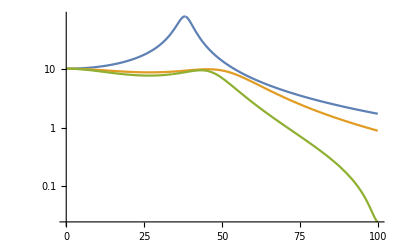

```mathematica
LogPlot[{Y1[2 π ⅈ s 10^6],Y2[2 π ⅈ s 10^6],Y3[2 π ⅈ s 10^6]},{s,0,100}]
```

#### Open-loop Transfer Function:

```mathematica
(* Use Kirchoff's rules to get transfer function, including inverting input impedance *)
Eliminate[Vin-Vs==Ic s Lc&&Vin-Vs==Ip/(s Cp)&& Vs==Is Rs&&Vs-Vi==Iff Rf&&Ic+Ip==Iff+Is&&Ie+Iff==Ig&&Vi==Ig (Rg+s Lg)&&Vi==-Ie Ri &&Vo==Ie Rt/(1+s Rt Ct),{Ic,Ip,Is,Ig,Iff,Ie,Vs, Vi}]
```

Rg ((Lc Rs Rt Vin)/(1+Ct Rt s)+(Rs Rt Vin)/(Cp s^2 (1+Ct Rt s))+Lc Rf Rs Vo+Lc Ri Rs Vo+(Rf Rs Vo)/(Cp s^2)+(Ri Rs Vo)/(Cp s^2)+(Lc Rf Vo)/(Cp s)+(Lc Ri Vo)/(Cp s)+(Lc Rs Vo)/(Cp s))==-(Lg Rs Rt Vin)/(Cp s (1+Ct Rt s))-(Lc Lg Rs Rt s Vin)/(1+Ct Rt s)-(Lc Lg Rf Vo)/Cp-(Lc Lg Ri Vo)/Cp-(Lc Lg Rs Vo)/Cp-Lc Rf Ri Rs Vo-(Rf Ri Rs Vo)/(Cp s^2)-(Lc Rf Ri Vo)/(Cp s)-(Lg Rf Rs Vo)/(Cp s)-(Lc Ri Rs Vo)/(Cp s)-(Lg Ri Rs Vo)/(Cp s)-Lc Lg Rf Rs s Vo-Lc Lg Ri Rs s Vo&&Cp≠0&&s≠0&&1+Ct Rt s≠0

```mathematica
Solve[Rg ((Lc Rs Rt Vin)/(1+Ct Rt s)+(Rs Rt Vin)/(Cp s^2 (1+Ct Rt s))+Lc Rf Rs Vo+Lc Ri Rs Vo+(Rf Rs Vo)/(Cp s^2)+(Ri Rs Vo)/(Cp s^2)+(Lc Rf Vo)/(Cp s)+(Lc Ri Vo)/(Cp s)+(Lc Rs Vo)/(Cp s))==-(Lg Rs Rt Vin)/(Cp s (1+Ct Rt s))-(Lc Lg Rs Rt s Vin)/(1+Ct Rt s)-(Lc Lg Rf Vo)/Cp-(Lc Lg Ri Vo)/Cp-(Lc Lg Rs Vo)/Cp-Lc Rf Ri Rs Vo-(Rf Ri Rs Vo)/(Cp s^2)-(Lc Rf Ri Vo)/(Cp s)-(Lg Rf Rs Vo)/(Cp s)-(Lc Ri Rs Vo)/(Cp s)-(Lg Ri Rs Vo)/(Cp s)-Lc Lg Rf Rs s Vo-Lc Lg Ri Rs s Vo,Vo]
```

{{Vo→(-(Lc Rg Rs Rt Vin)/(1+Ct Rt s)-(Rg Rs Rt Vin)/(Cp s^2 (1+Ct Rt s))-(Lg Rs Rt Vin)/(Cp s (1+Ct Rt s))-(Lc Lg Rs Rt s Vin)/(1+Ct Rt s))/((Lc Lg Rf)/Cp+(Lc Lg Ri)/Cp+(Lc Lg Rs)/Cp+Lc Rf Rg Rs+Lc Rf Ri Rs+Lc Rg Ri Rs+(Rf Rg Rs)/(Cp s^2)+(Rf Ri Rs)/(Cp s^2)+(Rg Ri Rs)/(Cp s^2)+(Lc Rf Rg)/(Cp s)+(Lc Rf Ri)/(Cp s)+(Lc Rg Ri)/(Cp s)+(Lg Rf Rs)/(Cp s)+(Lc Rg Rs)/(Cp s)+(Lc Ri Rs)/(Cp s)+(Lg Ri Rs)/(Cp s)+Lc Lg Rf Rs s+Lc Lg Ri Rs s)}}

```mathematica
Simplify[(-Rg(Lc Rf Rs Vo+Lc Ri Rs Vo+(Rf Rs Vo)/(Cp s^2)+(Ri Rs Vo)/(Cp s^2)+(Lc Rf Vo)/(Cp s)+(Lc Ri Vo)/(Cp s)+(Lc Rs Vo)/(Cp s))-(Lc Lg Rf Vo)/Cp-(Lc Lg Ri Vo)/Cp-(Lc Lg Rs Vo)/Cp-Lc Rf Ri Rs Vo-(Rf Ri Rs Vo)/(Cp s^2)-(Lc Rf Ri Vo)/(Cp s)-(Lg Rf Rs Vo)/(Cp s)-(Lc Ri Rs Vo)/(Cp s)-(Lg Ri Rs Vo)/(Cp s)-Lc Lg Rf Rs s Vo-Lc Lg Ri Rs s Vo)/Vo]
Simplify[(Rg ((Lc Rs Rt Vin)/(1+Ct Rt s)+(Rs Rt Vin)/(Cp s^2 (1+Ct Rt s)))-(-(Lg Rs Rt Vin)/(Cp s (1+Ct Rt s))-(Lc Lg Rs Rt s Vin)/(1+Ct Rt s)))/Vin]
```

-1/(Cp s^2)(Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Lc Rs s+Ri (Rs+Lc s+Cp Lc Rs s^2))+s (Lg Ri Rs+Lc Lg Rs s+Lc Ri (Rs+Lg s+Cp Lg Rs s^2)))

(Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/(s^2 (Cp+Cp Ct Rt s))

```mathematica
FullSimplify[((Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/(s^2 (Cp+Cp Ct Rt s)))/(-1/(Cp s^2)(Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Lc Rs s+Ri (Rs+Lc s+Cp Lc Rs s^2))+s (Lg Ri Rs+Lc Lg Rs s+Lc Ri (Rs+Lg s+Cp Lg Rs s^2))))]
```

-((Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/((1+Ct Rt s) (Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Ri Rs+Lc (Ri+Rs) s+Cp Lc Ri Rs s^2)+s ((Lc+Lg) Ri Rs+Lc Lg (Ri+Rs) s+Cp Lc Lg Ri Rs s^2))))

```mathematica
FullSimplify[(-(Lc Rg Rs Rt Vin)/(1+Ct Rt s)-(Rg Rs Rt Vin)/(Cp s^2 (1+Ct Rt s))-(Lg Rs Rt Vin)/(Cp s (1+Ct Rt s))-(Lc Lg Rs Rt s Vin)/(1+Ct Rt s))/((Lc Lg Rf)/Cp+(Lc Lg Ri)/Cp+(Lc Lg Rs)/Cp+Lc Rf Rg Rs+Lc Rf Ri Rs+Lc Rg Ri Rs+(Rf Rg Rs)/(Cp s^2)+(Rf Ri Rs)/(Cp s^2)+(Rg Ri Rs)/(Cp s^2)+(Lc Rf Rg)/(Cp s)+(Lc Rf Ri)/(Cp s)+(Lc Rg Ri)/(Cp s)+(Lg Rf Rs)/(Cp s)+(Lc Rg Rs)/(Cp s)+(Lc Ri Rs)/(Cp s)+(Lg Ri Rs)/(Cp s)+Lc Lg Rf Rs s+Lc Lg Ri Rs s)/Vin]
```

-((Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/((1+Ct Rt s) (Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Ri Rs+Lc (Ri+Rs) s+Cp Lc Ri Rs s^2)+s ((Lc+Lg) Ri Rs+Lc Lg (Ri+Rs) s+Cp Lc Lg Ri Rs s^2))))

```mathematica
(-((Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/((1+Ct Rt s) (Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Ri Rs+Lc (Ri+Rs) s+Cp Lc Ri Rs s^2)+s ((Lc+Lg) Ri Rs+Lc Lg (Ri+Rs) s+Cp Lc Lg Ri Rs s^2)))))/(-((Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/((1+Ct Rt s) (Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Ri Rs+Lc (Ri+Rs) s+Cp Lc Ri Rs s^2)+s ((Lc+Lg) Ri Rs+Lc Lg (Ri+Rs) s+Cp Lc Lg Ri Rs s^2)))))
```

1

```mathematica
Simplify[(-((Rs Rt (Rg+Lg s) (1+Cp Lc s^2))/((1+Ct Rt s) (Rf (Rg+Ri+Lg s) (Rs+Lc s+Cp Lc Rs s^2)+Rg (Ri Rs+Lc (Ri+Rs) s+Cp Lc Ri Rs s^2)+s ((Lc+Lg) Ri Rs+Lc Lg (Ri+Rs) s+Cp Lc Lg Ri Rs s^2)))))/.s->0]
```

-(Rg Rt)/(Rg Ri+Rf (Rg+Ri))

### To Litz or not to Litz

```mathematica
μ0=4 π 10^-7;
μc=μ0 1.26 10^-6;
delta[f_]:=Sqrt[2 1.68 10^-8/(2 π f μc)];
delta2[f_]:=503 Sqrt[1.68 10^-8/f] 10^6;
```

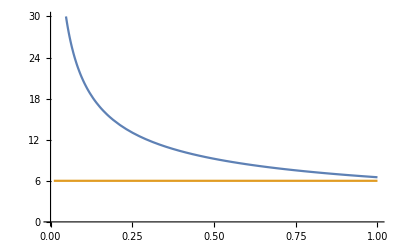

```mathematica
Plot[{delta2[f],6},{f,10^6,10^8},PlotRange->{0,30}]
```

```mathematica
Ap[w_,f_]:=If[2 delta2[f]<35,2 delta2[f] (35-2 delta2[f])+2 delta2[f] w,1];
Al[w_,f_,Nc_]:=If[2 delta2[f]<35,2 delta2[f] (35-2 delta2[f]) Nc+2 delta2[f] w,1];
```

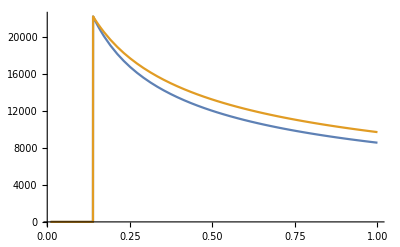

```mathematica
Plot[{Ap[5*127,f],Al[5*127,f,5]},{f,10^6,10^8}]
```

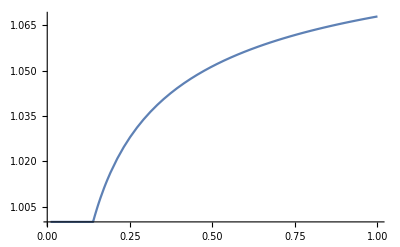

```mathematica
Plot[{Al[5*254,f,5]/Ap[5*254,f]},{f,10^6,10^8}]
```

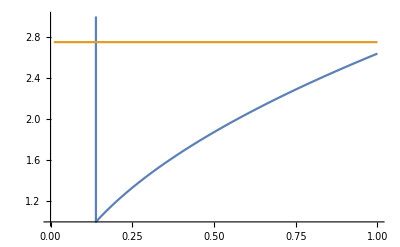

```mathematica
Plot[{35*5*254/Ap[5*254,f],2.75},{f,10^6,10^8},PlotRange->{1,3}]
```

```mathematica
Solve[77.3==Sqrt[(150*10^-9/200)/cc],cc]
200*cc /.%
```

{{cc→1.25517×10^-13}}

{2.51034×10^-11}

```mathematica
.015*1.4
```

0.021

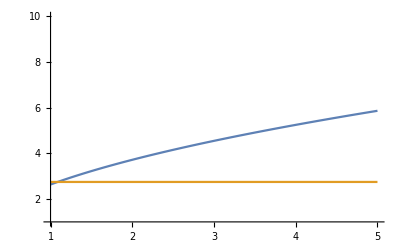

```mathematica
Plot[{35*50*25.4/Ap[50*25.4,f],2.75},{f,10^8,5 10^8},PlotRange->{1,10}]
```

## Microwave Antenna Design

```mathematica
c=3*^8;(*m/s*)
H=1.5*^-3;(*FR4 thickness, m*)
Er=3.9;(*FR4 dielectric constant*)
eta=376.7;(*impedance of free space, ohms*)
Er2=2.55;
H2=1.6*^-3;
```

### λ/2 patch first pass

```mathematica
w[f_,er_]:=c/(2 f Sqrt[er]);(*First width estimate, m*)
eff[f_,er_,h_]:=(er+1)/2+(er-1)/2 (1+(10h)/w[f,er])^(-1/2);(*effective dielectric constant*)
Δ[f_,er_,h_]:=0.412 h (eff[f,er,h]+0.300)/(eff[f,er,h]-0.258)(w[f,er]/h+0.262)/(w[f,er]/h+0.813);(*length correction, m*)
L[f_,er_,h_]:=c/(2 f Sqrt[eff[f,er,h]])-2 Δ[f,er,h];(*resonant length, m*)
G[f_,er_,h_]:=(π L[f,er,h])/(eta c/f) (1-(2 π f h/c)^2/24);(*Conductance of side slot, siemens*)
R[f_,er_,h_]:=1/(2 G[f,er,h]);(*Input impedance of patch, ohms*)
x[f_,er_,h_]:=L[f,er,h]/π ArcSin[(50/R[f,er,h])^(1/4)];(*50 ohm feedpoint, m from center*)
```

```mathematica
(* Check against example in text *)
w[3*^9,Er2]*1000
eff[3*^9,Er2,H2]
L[3*^9,Er2,H2]*1000
x[3*^9,Er2,H2]*1000
```

31.3112

2.40548

30.622

7.70664

```mathematica
(* 6.8 GHz for 87Rb *)
w[6.6*^9,Er]*1000
eff[6.6*^9,Er,H]
L[6.6*^9,Er,H]*1000
x[6.6*^9,Er,H]*1000
```

11.5084

3.4054

10.9552

2.55689

```mathematica
(* 3.0 GHz for 85Rb*)
w[2.9*^9,Er]*1000
eff[2.9*^9,Er,H]
L[2.9*^9,Er,H]*1000
x[2.9*^9,Er,H]*1000
```

26.1915

3.60623

25.8389

6.10009

### λ\2 patch 2nd pass

```mathematica
(*Use recursion to get better info*)
eff2[f_,er_,h_]:=(er+1)/2+(er-1)/2 (1+(10h)/L[f,er,h])^(-1/2);
Δ2[f_,er_,h_]:=0.412 h (eff2[f,er,h]+0.300)/(eff2[f,er,h]-0.258)(L[f,er,h]/h+0.262)/(L[f,er,h]/h+0.813);
L2[f_,er_,h_]:=c/(2 f Sqrt[eff2[f,er,h]])-2 Δ2[f,er,h];
G2[f_,er_,h_]:=(π L2[f,er,h])/(eta c/f) (1-(2 π f h/c)^2/24);(*Conductance of side slot, siemens*)
R2[f_,er_,h_]:=1/(2 G2[f,er,h]);(*Input impedance of patch, ohms*)
x2[f_,er_,h_]:=L2[f,er,h]/π ArcSin[(50/R2[f,er,h])^(1/4)];
```

```mathematica
(* Check example in text *)
eff2[3*^9,Er2,H2]
L2[3*^9,Er2,H2]*1000
```

2.40309

30.6386

```mathematica
(* 6.8 GHz for Rb *)
eff2[6.6*^9,Er,H]
L2[6.6*^9,Er,H]*1000
x2[6.6*^9,Er,H]*1000
```

3.39203

10.9828

2.56533

```mathematica
(* 3.0 GHz for 85Rb*)
eff2[2.9*^9,Er,H]
L2[2.9*^9,Er,H]*1000
x2[2.9*^9,Er,H]*1000
```

3.60337

25.8502

6.10356

### λ/4 patch

```mathematica
R4[f_,er_,h_]:=1/(G2[f,er,h]);(*Input impedance of patch, ohms*)
x4[f_,er_,h_]:=L2[f,er,h]/π ArcSin[(50/R4[f,er,h])^(1/4)];
```

```mathematica
(* 6.8 GHz for Rb *)
R4[6.8*^9,Er,H]
x4[6.8*^9,Er,H]*1000
```

498.238

2.02425

```mathematica
(* 3.0 GHz for Rb *)
R4[2.9*^9,Er,H]
x4[2.9*^9,Er,H]*1000
```

480.016

4.97159

### Curved Dipole

```mathematica
Ld[f_,er_]:=c/(4 f Sqrt[er]);(* Length of dipole leg, m*)
λeff[f_,er_]:=c/(f Sqrt[er]);(* Effective wavelength, m*)
```

```mathematica
Ld[800*^6,1]//N
```

0.09375

#### Lithium-7

```mathematica
Ld[800*^6,Er]
```

0.0474722

```mathematica
λeff[800*^6,Er]
```

0.189889

```mathematica
2 π 1.22 2.54
```

19.4703

#### Lithium-6

```mathematica
Ld[230*^6,Er]
Ld[230*^6,4.5]
```

0.165121

0.153719

```mathematica
R
```

```mathematica
λeff[230*^6,Er]
```

0.660482

```mathematica
2 π 1.22 2.54
```

19.4703

### Ring Impedance Matching

```mathematica
Solve[(1+(R1+ⅈ s L) ⅈ s C1)/(R1+ⅈ s L1)==0,{s}]
```

{{s→-(-ⅈ C1 R1-√(4 C1 L-C1^2 R1^2))/(2 C1 L)},{s→-(-ⅈ C1 R1+√(4 C1 L-C1^2 R1^2))/(2 C1 L)}}

```mathematica
Simplify[(-(-ⅈ C1 R1-√(4 C1 L-C1^2 R1^2))/(2 C1 L)) (-(ⅈ C1 R1-√(4 C1 L-C1^2 R1^2))/(2 C1 L))]
Simplify[(-(-ⅈ C1 R1+√(4 C1 L-C1^2 R1^2))/(2 C1 L)) (-(ⅈ C1 R1+√(4 C1 L-C1^2 R1^2))/(2 C1 L))]
```

1/(C1 L)

1/(C1 L)

```mathematica
Solve[(R1+ⅈ s L1+1/(ⅈ s C1))/((R1+ⅈ s L1)/(ⅈ s C1))==0,{s}]
```

{{s→-(ⅈ (-C1 R1+√C1 √(-4 L1+C1 R1^2)))/(2 C1 L1)},{s→(ⅈ (C1 R1+√C1 √(-4 L1+C1 R1^2)))/(2 C1 L1)}}

```mathematica
Solve[((R1+ⅈ s L1)/(ⅈ s C1))/(R1+ⅈ s L1+1/(ⅈ s C1))==0,{s}]
```

{{s→(ⅈ R1)/L1}}

```mathematica
Simplify[(R1+ⅈ s L1+1/(ⅈ s C1))/((R1+ⅈ s L1)/(ⅈ s C1)) (R1-ⅈ s L1-1/(ⅈ s C1))/((R1-ⅈ s L1)/(-ⅈ s C1))]
```

(1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2)

```mathematica
Simplify[Sqrt[(1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2)]]
```

√((1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2))

```mathematica
Solve[√((1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2))==0,{s}]
```

{{s→-(√(2/(C1 L1)-R1^2/L1^2-(R1 √(-4 L1+C1 R1^2))/(√C1 L1^2)))/(√2)},{s→(√(2/(C1 L1)-R1^2/L1^2-(R1 √(-4 L1+C1 R1^2))/(√C1 L1^2)))/(√2)},{s→-√(1/(C1 L1)-R1^2/(2 L1^2)+(R1 √(-4 L1+C1 R1^2))/(2 √C1 L1^2))},{s→√(1/(C1 L1)-R1^2/(2 L1^2)+(R1 √(-4 L1+C1 R1^2))/(2 √C1 L1^2))}}

```mathematica
FullSimplify[(√(2/(C1 L1)-R1^2/L1^2-(R1 √(-4 L1+C1 R1^2))/(√C1 L1^2)))/(√2)]
```

√2 √(1/(2 C1 L1-C1^2 R1^2+C1^(3/2) R1 √(-4 L1+C1 R1^2)))

```mathematica
C1[ω_,L_,R_]:=Sqrt[R/50]/(ω^2 L)
C2[ω_,L_,R_]:=(1-Sqrt[R/50])/(ω^2 L)
```

```mathematica
C1[2 π 130*^6,160*^-9,0.1]
C2[2 π 130*^6,160*^-9,0.1]
```

4.18937×10^-13

8.94878×10^-12

### Rabi Frequency

```mathematica
μb=1.4*^3;(*Bohr Magneton, kHz/G*)
gf=1/2;(*For alkali boson gs*)
Ω[B_]:=gf μb B;(* kHz *)
```

```mathematica
Ω[32*^-3]
```

22.4

## Loop antenna design

```mathematica
μ0=4 π 10^-7; (*H/m*)
r0=1.22*.0254;(*loop radius in m*)
w=0.05*.0254;(*loop width in m*)
h=35*^-6;(*loop height in m*)
ρ=1.68 10^-8;(*copper resistivity, Ohm*m*)
d=4.15 10^-2/2;(* distance of atoms from antenna in m*)
```

### Impedance

```mathematica
w//N
```

0.00127

```mathematica
Solve[w*h==π r^2,r]
```

{{r→-0.000118949},{r→0.000118949}}

```mathematica
wr=1.2*^-4;(*effective wire radius of loop*)
```

```mathematica
La[a_,b_]:=μ0 a (Log[8 a/b]-2)(*external reactance, loop radius a, wire radius b*)
Li[a_,b_,f_]:=(a/(2 π f b)) Sqrt[2 π f μ0 ρ/2]
```

```mathematica
La[r0,wr]
Li[r0,wr,1 10^6]
```

2.291×10^-7

1.05844×10^-8

```mathematica
hs=delta2[100*^6]/10^6
Solve[2 w hs==π r^2,r]
```

6.51963×10^-6

{{r→-0.0000726028},{r→0.0000726028}}

```mathematica
ws=72*^-6;
```

```mathematica
La[r0,ws]
Li[r0,ws,1 10^6]
```

2.39257×10^-7

1.76407×10^-8

```mathematica
2 w+2 h
2 π wr
```

0.00261

0.000753982

```mathematica
La[r0,h]
Li[r0,h,1 10^6]
```

2.67345×10^-7

3.62894×10^-8

```mathematica
2 π r0 ρ/(w h)
```

0.0735887

```mathematica
2 π r0 ρ/(π h^2)
```

0.849957

```mathematica
R[a_,b_,f_]:=2 π a ρ/(π (delta2[f]/1*^6) (2 b-delta2[f]/1*^6))
```

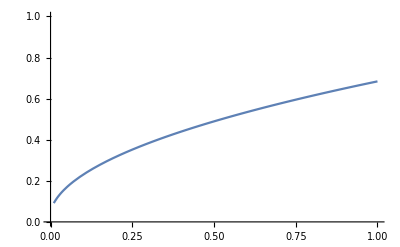

```mathematica
Plot[R[r0,wr,f],{f,1*^6, 100*^6},PlotRange->{0,1}]
```

### Loop Field

```mathematica
Bloop[I_,R_,z_]:=(μ0/(4 π)) (2 π I R^2/(z^2+R^2)^(3/2))
```

```mathematica
Bloop[0.1,r0,d] 10^4 (* in Gauss *)
```

0.0116322

```mathematica
μb=1.4*^3;(*Bohr Magneton, kHz/G*)
gf=1/2;(*For alkali boson gs*)
Ω[B_]:=gf μb B;(* kHz *)
```

```mathematica
Ω[Bloop[0.1,r0,d] 10^4 ]
```

8.14253

### D Field

```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Define the coil properties *)
(* Next, define their position: *)
z0=41.5/2; (* min z position of D coil *)
x0=0.; (* min x position of X shim *)
y0=0.;(* min y position of X shim *)

r0 = 1.29*25.4; (* inner radius of the D coil *)
r2 = 2.08*25.4;(* outer radius of the D coil *)
w=0.05*25.4;(*loop width in mm*)
h=35*^-3;(*loop height in mm*)
n=10;
jD = 0.15/w/h;
```

```mathematica
RotZ = radTrfRot[{0,0,0},{0,0,1},25*π/180];
RotZ2 = radTrfRot[{0,0,0},{0,0,1},-25*π/180];
arc1=radTrfOrnt[radObjArcCur[{0,0,z0+h/2},{r0-w/2,r0+w/2},{0,50 π/180},h,n,jD], RotZ2];
arc2=radTrfOrnt[radObjArcCur[{0,0,z0+h/2},{r2-w/2,r2+w/2},{0,50 π/180},h,n,-jD],RotZ2];
leg1 = radObjRecCur[{(r2-r0)/2+r0,0,z0+h/2},{r2-r0-w,w,h},{jD,0,0}];
radTrfOrnt[leg1,RotZ];
leg2 = radObjRecCur[{(r2-r0)/2+r0,0,z0+h/2},{r2-r0-w,w,h},{-jD,0,0}];
radTrfOrnt[leg2,RotZ2];
GrpD = radObjCnt[{arc1, arc2, leg1, leg2}];
RotZ3=radTrfRot[{0,0,0},{0,0,1},π];
RotInv=radTrfCmbL[RotZ3,radTrfInv[]];
radTrfMlt[GrpD, RotInv, 2];
RotX=radTrfRot[{0,0,0},{1,0,0},π];
radTrfMlt[GrpD,RotX,2]
```

17

```mathematica
(*Special Options for the Plot[]*)
RadPlot3DOptions[];

(*Save the Geometry in "dr"*)
drD=radObjDrw[GrpD];

(*Draw the Geometry*)
Show[Graphics3D[drD,PlotLabel->"D antenna",BaseStyle->{14,FontFamily->"Times"}]]
```

-Graphics3D-

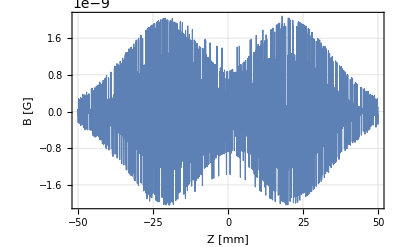

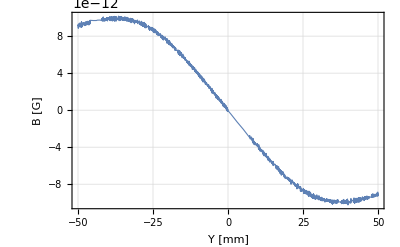

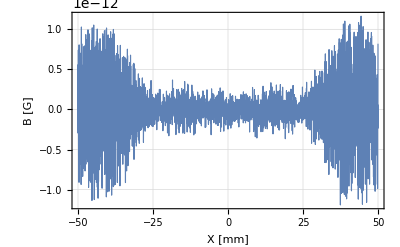

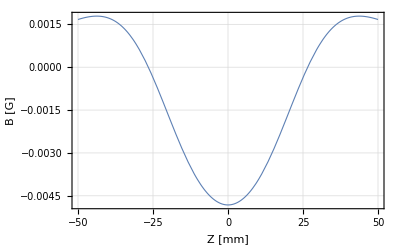

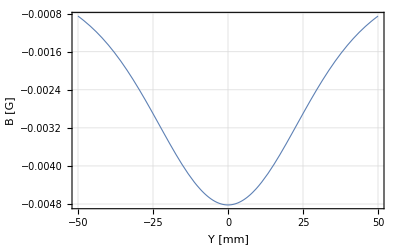

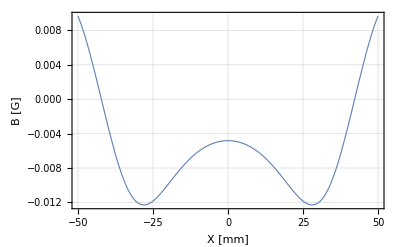

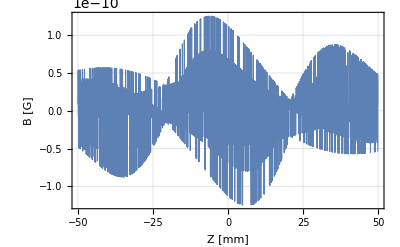

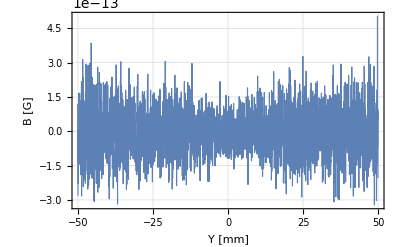

```mathematica
RadPlotOptions[];
Plot[10^4 radFld[GrpD,"bz",{0,0,z}],{z,-50,50},FrameLabel->{"Z [mm]","B [G]","X = Y = 0",""}]
Plot[10^4 radFld[GrpD,"bz",{0,y,0}],{y,-50,50},FrameLabel->{"Y [mm]","B [G]","X = Z = 0",""}]
Plot[10^4 radFld[GrpD,"bz",{x,0,0}],{x,-50,50},FrameLabel->{"X [mm]","B [G]","Y = Z = 0",""}]
Plot[10^4 radFld[GrpD,"bx",{0,0,z}],{z,-50,50},FrameLabel->{"Z [mm]","B [G]","X = Y = 0",""}]
Plot[10^4 radFld[GrpD,"bx",{0,y,0}],{y,-50,50},FrameLabel->{"Y [mm]","B [G]","X = Z = 0",""}]
Plot[10^4 radFld[GrpD,"bx",{x,0,0}],{x,-50,50},FrameLabel->{"X [mm]","B [G]","Y = Z = 0",""}]
Plot[10^4 radFld[GrpD,"by",{0,0,z}],{z,-50,50},FrameLabel->{"Z [mm]","B [G]","X = Y = 0",""}]
Plot[10^4 radFld[GrpD,"by",{0,y,0}],{y,-50,50},FrameLabel->{"Y [mm]","B [G]","X = Z = 0",""}]
Plot[10^4 radFld[GrpD,"by",{x,0,0}],{x,-50,50},FrameLabel->{"X [mm]","B [G]","Y = Z = 0",""}]
```

Radia::Error000: Incorrect input: Function arguments.

General::stop: Further output of Radia::Error000 will be suppressed during this calculation.

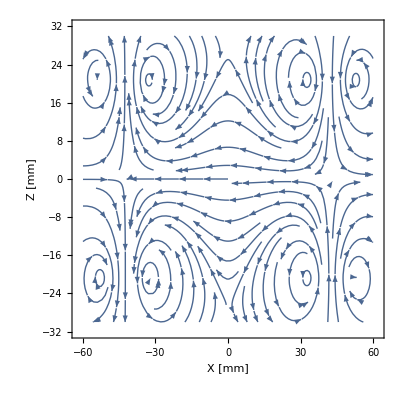

```mathematica
StreamPlot[{10^4 radFld[GrpD,"bx",{x,0,z}],10^4 radFld[GrpD,"bz",{x,0,z}]},{x,-60,60},{z,-30,30},FrameLabel->{"X [mm]","Z [mm]","Y = 0",""}]
```